```mathematica
datoteka="C:\\Users\\fs08767\\_Osebno\\iekg.xlsx";

podatki=Import[datoteka,{"Data",1}];


podatki2=podatki[[All,{1,2}]];
```

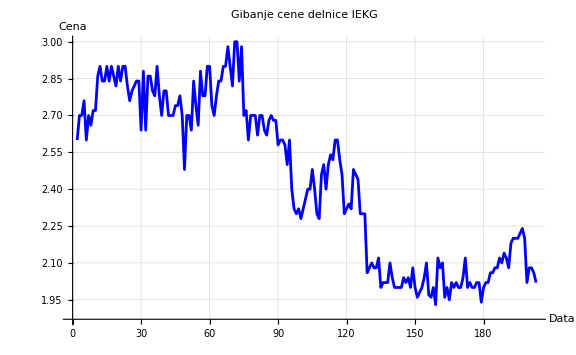

```mathematica
graf=ListLinePlot[podatki2,Joined->True,PlotStyle->Blue,AxesLabel->{"Data","Cena"},PlotLabel->"Gibanje cene delnice IEKG",GridLines->Automatic,ImageSize->Large];

graf
```

```mathematica
povprecnaCena=Total[podatki2[[2;;,2]]]/Length[podatki2[[2;;,2]]];
povprecnaCena
```

2.43916

```mathematica
rasti=Select[Transpose[{podatki2[[1;;-2,2]],podatki2[[2;;,2]]}],#[[2]]>#[[1]]&];

obdobjaRasti=Length[rasti]
```

82

```mathematica
padanja=Select[Transpose[{podatki2[[1;;-2,2]],podatki2[[2;;,2]]}],#[[2]]<#[[1]]&];

obdobjaPadanja=Length[padanja]
```

79

```mathematica
SeedRandom[42];
indeksNakupa=RandomInteger[{1,Length[podatki2]}];
cenaNakupa=podatki2[[indeksNakupa,2]];

indeksProdaje=RandomInteger[{indeksNakupa+1,Length[podatki2]}];
cenaProdaje=podatki2[[indeksProdaje,2]];

dobicek=cenaProdaje-cenaNakupa;

If[dobicek>0,"Na koncu si v plusu, dobiček: "<>ToString[dobicek],"Na koncu si v minusu, izguba: "<>ToString[Abs[dobicek]]]
```

Na koncu si v plusu, dobiček: 0.1